# Modificación de Imágenes, Desarrollo de Taylor y Errores

Mario Jacob García Navarro - A01363206

Tecnológico de Monterrey

## Modificación de Imágenes

## Primer Imagen (BioShock Infinite)

```mathematica
image01 = Import["http://fc01.deviantart.net/fs70/i/2013/101/7/7/_bioshock_infinite__columbia_by_sirleo09-d617amv.png"];
```

Imagen Original

-Graphics-

```mathematica
imageData01 = image01//ImageData;
imageData01//Dimensions
```

{720,1280,3}

```mathematica
Image[
Table[{imageData01[[i]][[j, 1]], imageData01[[i]][[j, 3]], imageData01[[i]][[j, 2]]}, {i, 1, 720}, {j, 1, 1280}]
]
```

Columbia Psicodélica

-Graphics-

```mathematica
Manipulate[Image[
Table[imageData01[[i]], {i, 1, j}]
], {j, 1,720}]
```

Generación de Imagen (Horizontal)

Part::partd: Part specification imageData01 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Image::imgarray: The specified argument {imageData01 ⟦ 1 ⟧, imageData01 ⟦ 2 ⟧, imageData01 ⟦ 3 ⟧, imageData01 ⟦ 4 ⟧, imageData01 ⟦ 5 ⟧, imageData01 ⟦ 6 ⟧, imageData01 ⟦ 7 ⟧, imageData01 ⟦ 8 ⟧, imageData01 ⟦ 9 ⟧, « 33 », imageData01 ⟦ 43 ⟧, imageData01 ⟦ 44 ⟧, imageData01 ⟦ 45 ⟧, imageData01 ⟦ 46 ⟧, imageData01 ⟦ 47 ⟧, imageData01 ⟦ 48 ⟧, imageData01 ⟦ 49 ⟧, imageData01 ⟦ 50 ⟧, « 561 »} should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification imageData01 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Image::imgarray: The specified argument {imageData01 ⟦ 1 ⟧, imageData01 ⟦ 2 ⟧, imageData01 ⟦ 3 ⟧, imageData01 ⟦ 4 ⟧, imageData01 ⟦ 5 ⟧, « 41 », imageData01 ⟦ 47 ⟧, imageData01 ⟦ 48 ⟧, imageData01 ⟦ 49 ⟧, imageData01 ⟦ 50 ⟧, « 561 »} should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification imageData01 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification imageData01 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Image::imgarray: The specified argument {imageData01 ⟦ 1 ⟧, imageData01 ⟦ 2 ⟧, imageData01 ⟦ 3 ⟧, imageData01 ⟦ 4 ⟧, imageData01 ⟦ 5 ⟧, imageData01 ⟦ 6 ⟧, imageData01 ⟦ 7 ⟧, imageData01 ⟦ 8 ⟧, imageData01 ⟦ 9 ⟧, imageData01 ⟦ 10 ⟧, imageData01 ⟦ 11 ⟧, imageData01 ⟦ 12 ⟧, « 27 », imageData01 ⟦ 40 ⟧, imageData01 ⟦ 41 ⟧, imageData01 ⟦ 42 ⟧, imageData01 ⟦ 43 ⟧, imageData01 ⟦ 44 ⟧, imageData01 ⟦ 45 ⟧, imageData01 ⟦ 46 ⟧, imageData01 ⟦ 47 ⟧, imageData01 ⟦ 48 ⟧, imageData01 ⟦ 49 ⟧, imageData01 ⟦ 50 ⟧, « 561 »} should be an array of rank 2 or 3 with machine-sized numbers.

Segunda Imagen (Middle-Earth: Shadow of Mordor)

```mathematica
image02 = Import["http://images.thisisxbox.com/2014/04/middle-earth-shadow-of-mordor-5.jpg"]
```

Imagen Original

-Graphics-

```mathematica
imageData02=ImageData[image02];
```

```mathematica
imageData02//Dimensions
```

{605,1200,3}

```mathematica
Image[
Table[{imageData02[[i]][[j, 3]], imageData02[[i]][[j, 2]], imageData02[[i]][[j, 2]]}, {i, 1, 605}, {j, 1, 1200}]
]
```

Gondor Bajo Luz Azul

-Graphics-

```mathematica
Manipulate[Image[
	Table[imageData02[[i]][[j]], {i, 1, 605}, {j, 1, k}]
	], {k, 1, 1200}
]
```

Generación de Imagen (Vertical)

Part::partd: Part specification imageData02 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of imageData02 ⟦ 1 ⟧ does not exist.

Part::partw: Part 4 of imageData02 ⟦ 1 ⟧ does not exist.

Part::partw: Part 5 of imageData02 ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Image::imgarray: The specified argument {{imageData02, 1, imageData02 ⟦ 1 ⟧ ⟦ 3 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 4 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 5 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 6 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 7 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 8 ⟧, « 35 », imageData02 ⟦ 1 ⟧ ⟦ 44 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 45 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 46 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 47 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 48 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 49 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 50 ⟧, « 215 »}, {« 1 »}, « 48 », « 555 »} should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification imageData02 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of imageData02 ⟦ 1 ⟧ does not exist.

Part::partw: Part 4 of imageData02 ⟦ 1 ⟧ does not exist.

Part::partw: Part 5 of imageData02 ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Image::imgarray: The specified argument {{imageData02, 1, imageData02 ⟦ 1 ⟧ ⟦ 3 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 4 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 5 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 6 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 7 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 8 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 9 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 10 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 11 ⟧, « 30 », imageData02 ⟦ 1 ⟧ ⟦ 42 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 43 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 44 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 45 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 46 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 47 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 48 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 49 ⟧, imageData02 ⟦ 1 ⟧ ⟦ 50 ⟧, « 215 »}, « 49 », « 555 »} should be an array of rank 2 or 3 with machine-sized numbers.

## Desarrollo de Taylor y Errores

Función Exponencial

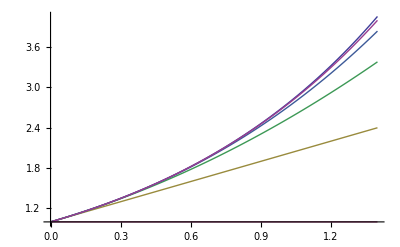

```mathematica
Plot[Tooltip[{ⅇ^x, 1, 1+x, 1+x+x^2/2, 1+x+x^2/2+x^3/6, 1+x+x^2/2+x^3/6+x^4/24 }], {x, 0, 1.4}]
```

```mathematica
(** Definiciones **) f[x_]:=ⅇ^x;xp=1.4;n=15;sumaprevia=0;
```

```mathematica
Do[Subscript[sumapresente, i] = sumaprevia+(xp)^i/(i!);
sumaprevia=Subscript[sumapresente, i], {i, 0, n}
];
Do[Subscript[errorverdadero, i]=f[xp]-Subscript[sumapresente, i];
Subscript[errorverdaderoabs, i]=Abs[f[xp]-Subscript[sumapresente, i]];
Subscript[errorverdaderorelativo, i]=(f[xp]-Subscript[sumapresente, i])/f[xp];
Subscript[errorverdaderorelativoporcentual, i]=Abs[(f[xp]-Subscript[sumapresente, i])/f[xp]*100];, {i, 0, n}
];
```

```mathematica
TableForm[Table[{i, f[xp],NumberForm[Subscript[sumapresente, i], {10, 10}], Subscript[errorverdadero, i], Subscript[errorverdaderoabs, i],Subscript[errorverdaderorelativo, i],Subscript[errorverdaderorelativoporcentual, i]},{i, 0, n}], TableHeadings->{None, {"i", "Valor Real", "Valor Aproximado", "E. Verdadero", "E.V. Absoluto", "E.V. Relativo", "E.V.R. Porcentual"}}]
```

i | Valor Real | Valor Aproximado | E. Verdadero | E.V. Absoluto | E.V. Relativo | E.V.R. Porcentual
0 | 4.0552 | 1.0000000000 | 3.0552 | 3.0552 | 0.753403 | 75.3403
1 | 4.0552 | 2.4000000000 | 1.6552 | 1.6552 | 0.408167 | 40.8167
2 | 4.0552 | 3.3800000000 | 0.6752 | 0.6752 | 0.166502 | 16.6502
3 | 4.0552 | 3.8373333330 | 0.217867 | 0.217867 | 0.0537253 | 5.37253
4 | 4.0552 | 3.9974000000 | 0.0578 | 0.0578 | 0.0142533 | 1.42533
5 | 4.0552 | 4.0422186670 | 0.0129813 | 0.0129813 | 0.00320115 | 0.320115
6 | 4.0552 | 4.0526763560 | 0.00252361 | 0.00252361 | 0.000622315 | 0.0622315
7 | 4.0552 | 4.0547678930 | 0.000432074 | 0.000432074 | 0.000106548 | 0.0106548
8 | 4.0552 | 4.0551339120 | 0.0000660544 | 0.0000660544 | 0.0000162888 | 0.00162888
9 | 4.0552 | 4.0551908490 | 9.11809×10^-6 | 9.11809×10^-6 | 2.24849×10^-6 | 0.000224849
10 | 4.0552 | 4.0551988200 | 1.14701×10^-6 | 1.14701×10^-6 | 2.82849×10^-7 | 0.0000282849
11 | 4.0552 | 4.0551998340 | 1.3251×10^-7 | 1.3251×10^-7 | 3.26765×10^-8 | 3.26765×10^-6
12 | 4.0552 | 4.0551999530 | 1.41512×10^-8 | 1.41512×10^-8 | 3.48965×10^-9 | 3.48965×10^-7
13 | 4.0552 | 4.0551999650 | 1.40493×10^-9 | 1.40493×10^-9 | 3.46452×10^-10 | 3.46452×10^-8
14 | 4.0552 | 4.0551999670 | 1.30304×10^-10 | 1.30304×10^-10 | 3.21325×10^-11 | 3.21325×10^-9
15 | 4.0552 | 4.0551999670 | 1.13385×10^-11 | 1.13385×10^-11 | 2.79604×10^-12 | 2.79604×10^-10

Función Coseno

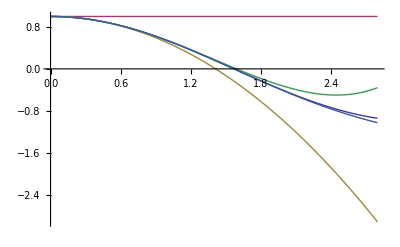

```mathematica
Plot[Tooltip[{Cos[x], 1, 1-x^2/2, 1-x^2/2+x^4/24,  1-x^2/2+x^4/24-x^6/720}], {x, 0, 2.8}]
```

```mathematica
(** Definiciones **) f[x_]:=Cos[x];xp=2.8;n=15;sumaprevia=0;
```

```mathematica
Do[Subscript[sumapresente, i] = sumaprevia+(-1)^i*(xp)^(2*i)/((2*i)!);
sumaprevia=Subscript[sumapresente, i], {i, 0, n}
];
Do[Subscript[errorverdadero, i]=f[xp]-Subscript[sumapresente, i];
Subscript[errorverdaderoabs, i]=Abs[f[xp]-Subscript[sumapresente, i]];
Subscript[errorverdaderorelativo, i]=(f[xp]-Subscript[sumapresente, i])/f[xp];
Subscript[errorverdaderorelativoporcentual, i]=Abs[(f[xp]-Subscript[sumapresente, i])/f[xp]*100];, {i, 0, n}
];
```

```mathematica
TableForm[Table[{i, f[xp],NumberForm[Subscript[sumapresente, i], {10, 10}], Subscript[errorverdadero, i], Subscript[errorverdaderoabs, i],Subscript[errorverdaderorelativo, i],Subscript[errorverdaderorelativoporcentual, i]},{i, 0, n}], TableHeadings->{None, {"i", "Valor Real", "Valor Aproximado", "E. Verdadero", "E.V. Absoluto", "E.V. Relativo", "E.V.R. Porcentual"}}]
```

i | Valor Real | Valor Aproximado | E. Verdadero | E.V. Absoluto | E.V. Relativo | E.V.R. Porcentual
0 | -0.942222 | 1.0000000000 | -1.94222 | 1.94222 | 2.06132 | 206.132
1 | -0.942222 | -2.9200000000 | 1.97778 | 1.97778 | -2.09906 | 209.906
2 | -0.942222 | -0.3589333333 | -0.583289 | 0.583289 | 0.619057 | 61.9057
3 | -0.942222 | -1.0282254220 | 0.0860031 | 0.0860031 | -0.0912768 | 9.12768
4 | -0.942222 | -0.9345245298 | -0.00769781 | 0.00769781 | 0.00816985 | 0.816985
5 | -0.942222 | -0.9426869186 | 0.000464578 | 0.000464578 | -0.000493066 | 0.0493066
6 | -0.942222 | -0.9422021222 | -0.0000202185 | 0.0000202185 | 0.0000214583 | 0.00214583
7 | -0.942222 | -0.9422230057 | 6.65072×10^-7 | 6.65072×10^-7 | -7.05854×10^-7 | 0.0000705854
8 | -0.942222 | -0.9422223235 | -1.71239×10^-8 | 1.71239×10^-8 | 1.81739×10^-8 | 1.81739×10^-6
9 | -0.942222 | -0.9422223410 | 3.54575×10^-10 | 3.54575×10^-10 | -3.76318×10^-10 | 3.76318×10^-8
10 | -0.942222 | -0.9422223407 | -6.03306×10^-12 | 6.03306×10^-12 | 6.40301×10^-12 | 6.40301×10^-10
11 | -0.942222 | -0.9422223407 | 8.63754×10^-14 | 8.63754×10^-14 | -9.16719×10^-14 | 9.16719×10^-12
12 | -0.942222 | -0.9422223407 | -5.55112×10^-16 | 5.55112×10^-16 | 5.89151×10^-16 | 5.89151×10^-14
13 | -0.942222 | -0.9422223407 | 4.44089×10^-16 | 4.44089×10^-16 | -4.71321×10^-16 | 4.71321×10^-14
14 | -0.942222 | -0.9422223407 | 4.44089×10^-16 | 4.44089×10^-16 | -4.71321×10^-16 | 4.71321×10^-14
15 | -0.942222 | -0.9422223407 | 4.44089×10^-16 | 4.44089×10^-16 | -4.71321×10^-16 | 4.71321×10^-14